Министерство образования и науки Российской Федерации
Федеральное государственное бюджетное образовательное учреждение
высшего профессионального образования
«Национальный исследовательский Томский политехнический университет»

Институт: ИЯТШ
Отделение прикладной математики и информатики





							
				
ОТЧЕТ ПО ЛАБОРАТОРНОЙ РАБОТЕ №5

 Основные понятия теории графов

Вариант №18

Выполнил студент группы 0В01:
Саматов Денис
Проверил: Шинкеев М.Л.

Томск 2021

Простой граф задан диаграммой (см . варианты задания на следущих страницах) . Требуется : 
	1) Задать граф в виде списка ребер . 
	2) Построить матрицы смежности и инцидентности.
	3) Построить матрицу расстояний между вершинами графа . 
	4) Найти диаметр графа, радиус графа, центр графа . Отобразить центр графа на
    графе.
	5) Найти простой цикл максимальной длины, проходящий через вершину w и
  отобразить его на графе . 
	6) Составить обходы графа в ширину и глубину, используя в качестве начальной
вершины - вершину w . Построить деревья обхода .
-Graphics-
1) Задать граф в виде списка ребер .

```mathematica
gr=Graph[{1<->6,6<->19,19<->17,5<->7,5<->10,7<->16,10<->16,10<->15,17<->15,10<->2,10<->4,16<->3,16<->13,3<->17,3<->15,13<->11,16<->11,13<->2,13<->18,11<->4,4<->2,15<->9,9<->18,18<->14,14<->8,8<->20,13<->12,12<->20,20<->11,11<->1,6<->5},VertexLabels->"Name"]
```

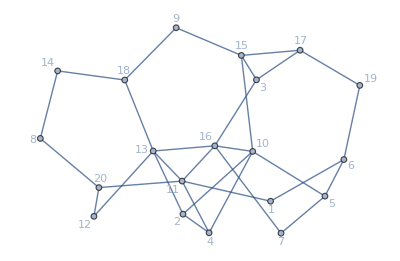

Set::write: Tag Inherited in Inherited[State] is Protected.

2) Построить матрицы смежности и инцидентности .

```mathematica
TableForm[Map[Normal,AdjacencyMatrix[gr]],TableHeadings->{VertexList[gr],VertexList[gr]}]
```

| 1 | 6 | 19 | 17 | 5 | 7 | 10 | 16 | 15 | 2 | 4 | 3 | 13 | 11 | 18 | 9 | 14 | 8 | 20 | 12
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
6 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
19 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
15 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1
11 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0

```mathematica
TableForm[Normal@IncidenceMatrix[gr],TableHeadings->{VertexList[gr],EdgeList[gr]}]
```

| 1<->6 | 6<->19 | 19<->17 | 5<->7 | 5<->10 | 7<->16 | 10<->16 | 10<->15 | 17<->15 | 10<->2 | 10<->4 | 16<->3 | 16<->13 | 3<->17 | 3<->15 | 13<->11 | 16<->11 | 13<->2 | 13<->18 | 11<->4 | 4<->2 | 15<->9 | 9<->18 | 18<->14 | 14<->8 | 8<->20 | 13<->12 | 12<->20 | 20<->11 | 11<->1 | 6<->5
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
6 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
19 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
7 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
13 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
20 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0
12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0

3) Построить матрицу расстояний между вершинами графа.

```mathematica
TableForm[GraphDistanceMatrix[gr],TableHeadings->{VertexList[gr],VertexList[gr]}]
```

| 1 | 6 | 19 | 17 | 5 | 7 | 10 | 16 | 15 | 2 | 4 | 3 | 13 | 11 | 18 | 9 | 14 | 8 | 20 | 12
1 | 0 | 1 | 2 | 3 | 2 | 3 | 3 | 2 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 4 | 4 | 3 | 2 | 3
6 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 4 | 4 | 5 | 4 | 3 | 4
19 | 2 | 1 | 0 | 1 | 2 | 3 | 3 | 3 | 2 | 4 | 4 | 2 | 4 | 3 | 4 | 3 | 5 | 5 | 4 | 5
17 | 3 | 2 | 1 | 0 | 3 | 3 | 2 | 2 | 1 | 3 | 3 | 1 | 3 | 3 | 3 | 2 | 4 | 5 | 4 | 4
5 | 2 | 1 | 2 | 3 | 0 | 1 | 1 | 2 | 2 | 2 | 2 | 3 | 3 | 3 | 4 | 3 | 5 | 5 | 4 | 4
7 | 3 | 2 | 3 | 3 | 1 | 0 | 2 | 1 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 4 | 4 | 4 | 3 | 3
10 | 3 | 2 | 3 | 2 | 1 | 2 | 0 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 3 | 2 | 4 | 4 | 3 | 3
16 | 2 | 3 | 3 | 2 | 2 | 1 | 1 | 0 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 3 | 3 | 3 | 2 | 2
15 | 4 | 3 | 2 | 1 | 2 | 3 | 1 | 2 | 0 | 2 | 2 | 1 | 3 | 3 | 2 | 1 | 3 | 4 | 4 | 4
2 | 3 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 2 | 0 | 1 | 3 | 1 | 2 | 2 | 3 | 3 | 4 | 3 | 2
4 | 2 | 3 | 4 | 3 | 2 | 3 | 1 | 2 | 2 | 1 | 0 | 3 | 2 | 1 | 3 | 3 | 4 | 3 | 2 | 3
3 | 3 | 3 | 2 | 1 | 3 | 2 | 2 | 1 | 1 | 3 | 3 | 0 | 2 | 2 | 3 | 2 | 4 | 4 | 3 | 3
13 | 2 | 3 | 4 | 3 | 3 | 2 | 2 | 1 | 3 | 1 | 2 | 2 | 0 | 1 | 1 | 2 | 2 | 3 | 2 | 1
11 | 1 | 2 | 3 | 3 | 3 | 2 | 2 | 1 | 3 | 2 | 1 | 2 | 1 | 0 | 2 | 3 | 3 | 2 | 1 | 2
18 | 3 | 4 | 4 | 3 | 4 | 3 | 3 | 2 | 2 | 2 | 3 | 3 | 1 | 2 | 0 | 1 | 1 | 2 | 3 | 2
9 | 4 | 4 | 3 | 2 | 3 | 4 | 2 | 3 | 1 | 3 | 3 | 2 | 2 | 3 | 1 | 0 | 2 | 3 | 4 | 3
14 | 4 | 5 | 5 | 4 | 5 | 4 | 4 | 3 | 3 | 3 | 4 | 4 | 2 | 3 | 1 | 2 | 0 | 1 | 2 | 3
8 | 3 | 4 | 5 | 5 | 5 | 4 | 4 | 3 | 4 | 4 | 3 | 4 | 3 | 2 | 2 | 3 | 1 | 0 | 1 | 2
20 | 2 | 3 | 4 | 4 | 4 | 3 | 3 | 2 | 4 | 3 | 2 | 3 | 2 | 1 | 3 | 4 | 2 | 1 | 0 | 1
12 | 3 | 4 | 5 | 4 | 4 | 3 | 3 | 2 | 4 | 2 | 3 | 3 | 1 | 2 | 2 | 3 | 3 | 2 | 1 | 0

4) Найти диаметр графа, радиус графа, центр графа . Отобразить центр графа на
    графе.

```mathematica
d=GraphDiameter[gr]
```

5

```mathematica
r=GraphRadius[gr]
```

3

```mathematica
HighlightGraph[gr,GraphCenter[gr]]
```

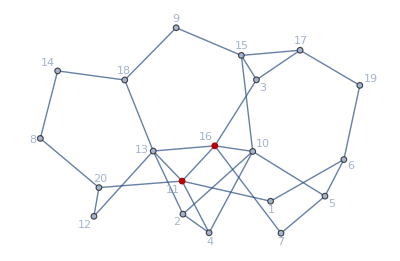

5) Найти простой цикл максимальной длины, проходящий через вершину w и
  отобразить его на графе.

```mathematica
HighlightGraph[gr,[FindCycle[{gr,1},Infinity,All]]]
```

```mathematica
FindCycle[{gr,1},Infinity,All];
```

```mathematica
f=Length[FindCycle[{gr,1},Infinity,All][[1]]];
```

```mathematica
For[i=1,i<=Length[FindCycle[{gr,1},Infinity,All]],i++,
If[Length[FindCycle[{gr,1},Infinity,All][[i]]]>f ,f=Length[FindCycle[{gr,1},Infinity,All][[i]]]]]
```

```mathematica
For[i=1,i<=Length[FindCycle[{gr,1},Infinity,All]],i++,
If[Length[FindCycle[{gr,1},Infinity,All][[i]]]==f ,f=FindCycle[{gr,1},Infinity,All][[i]]]]
```

```mathematica
f
```

{1<->6,6<->19,19<->17,17<->3,3<->15,15<->9,9<->18,18<->14,14<->8,8<->20,20<->12,12<->13,13<->16,16<->7,7<->5,5<->10,10<->2,2<->4,4<->11,11<->1}

```mathematica
HighlightGraph[gr,f]
```

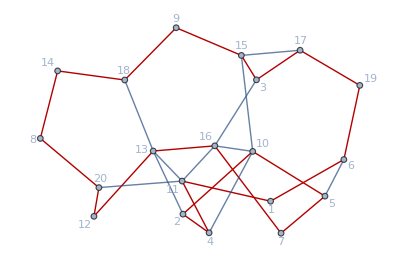

6) Составить обходы графа в ширину и глубину, используя в качестве начальной
вершины - вершину w . Построить деревья обхода.

```mathematica
HighlightGraph[gr,Reap[BreadthFirstScan[gr, 1, {"FrontierEdge" -> Sow}]][[2, 1]]]
```

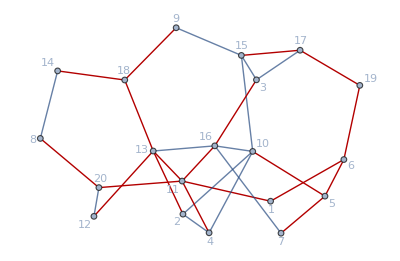

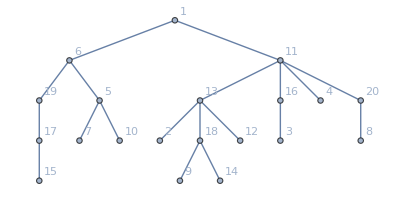

```mathematica
TreeGraph[First[Last[Reap[BreadthFirstScan[gr, 1, {"FrontierEdge" -> Sow}]]]], VertexLabels->"Name"]
```

```mathematica
HighlightGraph[gr,Reap[DepthFirstScan[gr, 1, {"FrontierEdge" -> Sow}]][[2, 1]]]
```

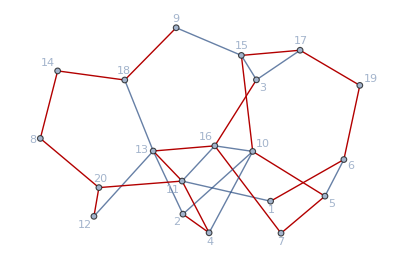

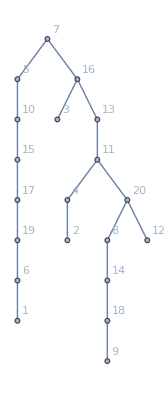

```mathematica
TreeGraph[First[Last[Reap[DepthFirstScan[gr, 1, {"FrontierEdge" -> Sow}]]]], VertexLabels->"Name"]
```